# Relaciones de Kramers Kronig

```mathematica
(*En este código se obtiene la parte real del índice de refracción/función dieléctrica empleando las relaciones de Kramers-Kronig*)
```

#### Modelo de Drude

```mathematica
omegaMin=0.5; (*valor mínimo de energía*)
omegaMax=10; (*valor máximo de energía*)
omega1=Range[omegaMin,omegaMax,0.01]; (*rango de energías*)
omegaPAl=13.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
(*Se define la parte real y la imaginaria del índice de refracción*)
nImagDrude[energy_,omegaP_,gamma_]:=Im[Sqrt[epsDrude[energy,omegaP,gamma]]]
nReDrude[energy_,omegaP_,gamma_]:=Re[Sqrt[epsDrude[energy,omegaP,gamma]]]
```

```mathematica
alRealDrude=Table[{omega,nReDrude[omega,omegaPAl,gammaAl]},{omega,0.01,10,0.01}];
alImagDrude=Table[{omega,nImagDrude[omega,omegaPAl,gammaAl]},{omega,0.01,10,0.01}];
```

```mathematica
(*Se calcula la parte imaginaria con KK*)
nReKK=Table[{w,1+(2/Pi)*NIntegrate[nImagDrude[x,omegaPAl,gammaAl]*x/(x^2-w^2),{x,0.01,w,10},Method->"PrincipalValue"]},{w,0.06,9.95,0.01}];
```

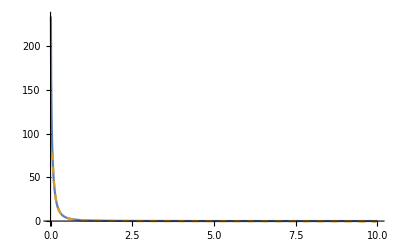

```mathematica
ListLinePlot[{alRealDrude,Style[nReKK,Dashed]},PlotRange->All]
```

#### Valores experimentales del silicio

```mathematica
datos0=Import["C:\\Users\\Poh\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,{1,21}];
(*Se interpolan los datos de la parte imaginaria*)
parteImPV=Interpolation[Transpose[{datos1[[All,1]],datos1[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
omega=datos1[[All,1]];
```

```mathematica
parteReKKPV=Table[{w,1.+(2/Pi)*NIntegrate[parteImPV[x]*x/(x^2-w^2),{x,0.5,w,6.},Method->"PrincipalValue"]},{w,omega[[2]],omega[[-2]],0.01}];
```

NIntegrate::inumri: The integrand ((2.9-x) «1»[2.9-x])/(-8.41+(2.9-x)^2)+((2.9+x) InterpolatingFunction[{{0.55,6.}},{5,7,0,{92},{4},0,0,0,0,Automatic,«3»},{{0.55,0.6,0.65,0.7,«3»,0.9,0.95,1.,«82»}},«1»,{Automatic}][«19»+x])/(-8.41+(2.9+x)^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,2.22045×10^-16}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

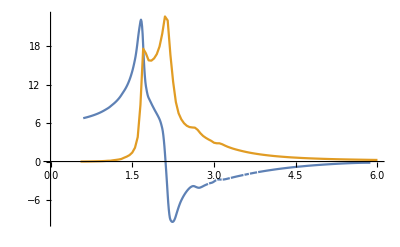

```mathematica
ListLinePlot[{parteReKKPV,parteImPV}]
```

#### Datos experimentales del Oro

```mathematica
h=4.135667696*10^(-15); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=Interpolation[Transpose[{ωAu,nau1[[All,2]]}]];
kAu=Interpolation[Transpose[{ωAu,kau1[[All,2]]}]];
```

```mathematica
nnau=Table[{w,nau[w]},{w,0.65,6.6,0.01}];
knau=Table[{w,kAu[w]},{w,0.65,6.6,0.01}];
```

```mathematica
parteReAuKK=Table[{w,1.+(2/Pi)*NIntegrate[kAu[x]*x/(x^2-w^2),{x,0.7,w,6.6},Method->"PrincipalValue"]},{w,ωAu[[-4]],ωAu[[4]],0.01}];
```

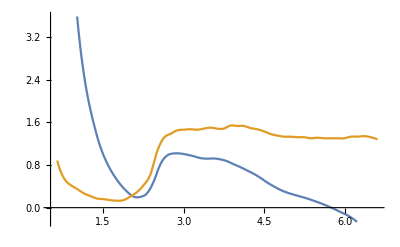

```mathematica
ListLinePlot[{parteReAuKK,nnau},PlotRange->All]
```

```mathematica
nImagDrude[energy_]:=Im[Sqrt[epsDrude[energy,omegaPAl,gammaAl]]]
nReDrude[energy_]:=Re[Sqrt[epsDrude[energy,omegaPAl,gammaAl]]]
```

```mathematica
hola=Table[{w,1+(2/Pi)*NIntegrate[nImagDrude[x]*x/(x^2-w^2),{x,0.01,w,10},Method->"PrincipalValue"]},{w,0.06,9.95,0.01}];
```

```mathematica
omega=Range[0.06,9.95,0.01];
```

```mathematica
nRealDrude2=Transpose[{omega,hola[[All,2]]}];
```

```mathematica
hola2=Table[{w,-(2/Pi)*NIntegrate[(nRealDrude2[x]-1)*x/(x^2-w^2),{x,0.01,w,10},Method->"PrincipalValue"]},{w,0.06,9.95,0.01}];
```

NIntegrate::inumr: The integrand (x (-1+{{0.06,77.9503},{0.07,67.7878},{0.08,59.5799},{0.09,52.784},«4»,{0.14,31.1511},{0.15,28.3627},«980»}[x]))/(-0.0036+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.01,0.035}}.

NIntegrate::inumr: The integrand (x (-1+{{0.06,77.9503},{0.07,67.7878},{0.08,59.5799},{0.09,52.784},«4»,{0.14,31.1511},{0.15,28.3627},«980»}[x]))/(-0.0036+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.085,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

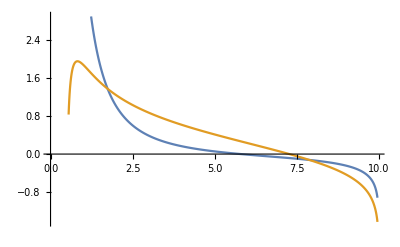

```mathematica
ListLinePlot[{hola1,hola2}]
```